# Distance between point and line

```mathematica
Subscript[x, P_]:=P[[1]];Subscript[y, P_]:=P[[2]];
```

```mathematica
P={-2,-2};
```

```mathematica
f[x_]=1/3 x+2;
```

```mathematica
A=Coefficient[f[x],x, 1];B=-1;𝒞=Coefficient[f[x],x, 0];
```

```mathematica
A x +B y+𝒞==0
```

2+x/3-y==0

```mathematica
d=Abs[A Subscript[x, P]+B Subscript[y, P]+𝒞]/(√(A^2+B^2))
```

√10

```mathematica
PointP=ListPlot[{P},PlotRange->{{-5,5},{-5,5}},MeshStyle->Red,PlotMarkers->{Automatic,Medium},AspectRatio->1];
```

```mathematica
LineD=Plot[f[x],{x,-5,5},PlotRange->{{-5,5},{-5,5}},AspectRatio->1];
```

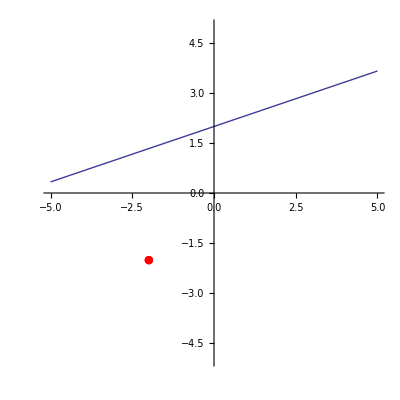

```mathematica
Show[PointP,LineD]
```